# The Ramsey Model of Economic Growth

by Alexander Tabarrok as modified by Chris Carroll

This notebook uses Mathematica to obtain a numerical solution to the Ramsey model of economic growth.  Introductions to the Ramsey model can be found in the texts of Romer (1996), Barro and Sala-i-Martin (1995), and Blanchard and Fischer (1989) and of course the original articles by Ramsey (1928), Cass (1965), and Koopmans (1965).  
	The solution methods used, the shooting and time elimination method, are of wide applicability to many problems in economics, requiring that we solve two paired differential equations with a boundary condition.

```mathematica
Off[General::spell];ClearAll["Global`*"];
```

```mathematica
profit=F[K,AL]- w AL - (r+δ) K
```

-AL w-K (r+δ)+F[K,AL]

To maximize profit the firm hires capital and labor until the first derivatives of the profit function with respect to capital and labor respectively are zero.

```mathematica
D[profit,K]==0
```

-r-δ+F^(1,0)[K,AL]==0

```mathematica
D[profit,AL]==0
```

-w+F^(0,1)[K,AL]==0

We will also assume that the production function F is linearly homogeneous or in economic terms that it exhibits constant returns to scale (CRS).The CRS assumption means that if inputs increase by a factor of c, output will also increase by a factor of c, F[cK,cAL]= cF[K,AL].  A theorem by Euler says that if F[K,AL] is linearly homogeneous, then Y=F_K K+F_AL AL.  Using the above first-order conditions, Euler's theorem implies that factor payments exhaust the product, Y=(r+δ )K+w AL.  Setting c=1/AL allows us to write the production function in terms of one variable, capital per unit of effective labor k=K/AL.  Thus, output per unit of effective labor can be written Y/AL=y=f[k].  Rewriting the first-order condition for capital we have
1)  r+δ=f'[k]
and using (1) and Euler's theorem
2) w=f[k]-kf'[k].

Household behavior is more complicated.  There are a large number, H, of identical households.  Each member of the household supplies 1 unit of labor at every point in time.  Households own the capital stock, which they rent to firms.  Each household begins with capital holdings of K[0]/H where K[t] is the amount of capital at time t.  At each moment in time the household chooses how to divide its income - from wages and the renting of capital - between consumption and savings in order to maximize lifetime utility.  The household's lifetime utility is written;

U=∫_0^∞ e^-θt u(C[t] /L[t]) dt

where C[t] is the consumption of each household member at time t. u[C[t]] is the instantaneous utility created by the consumption of C[t] at time t.  L[t] is the total population of the economy and L[t]/H the number of members of the household at time t.  θ>0 is the household's discount rate (assumed the same for all households).  The higher is θ the more the household discounts future consumption relative to current consumption.  It is common to assume that instantaneous utility is of the form u(C[t])=C[t]^(1-ρ)/(1-ρ), with ρ>0 and θ-(1-ρ)g>0.  ρ governs how willing individuals are to substitute consumption from one time period into another.  A lower ρ implies a greater willingness to substitute consumption tomorrow for consumption today.   The condition θ-n-(1-ρ)g>0 is a technical condition needed to ensure that utility is bounded below infinity.  It's convenient to write the budget constraint in terms of consumption per unit of effective labor.  After some algebraic manipulations and taking into account the fact that L and A are growing we have (see Romer (1996) for the derivation).

U=B∫_0^∞ e^-νt c[t]^(1-ρ)/(1-ρ) dt

where B=A[0]^(1-ρ)L[0]/H and ν=θ-(1-ρ)g.

B is an unimportant constant and will be normalized to 1 in what follows.

The household faces two constraints when maximizing utility.

1)  k'[t]=r[t] k[t] + e^((n+g)t)(w[t]-c[t])

2)  Lim_(t⟶∞) e^(-R[t])e^((n+g)t)k[t]≥0,

where R[t]=∫_0^t r[τ]dτ.

The first constraint is closer to an accounting identity than a constraint it that it says that the growth in the household's capital stock (per unit of effective labor) is equal to the interest earnings on the current capital stock plus the difference between the household's wages in period t and its consumption in period t (the exponential term adjusts for growth in effective labor).   Notice that 1) does not forbid the household from consuming more than its wages by borrowing (creating a negative capital stock).  It follows that the optimal solution to the household's problem is to borrow an infinite amount and live it up!  Since the latter strategy is unrealistic, we need constraint 2, which says that the household's capital stock (adjusted per unit of effective labor) cannot be negative in the limit.  In other words, the household must live within its means, if not on any given day then in the limit.

The household's problem has been set up as a standard problem in optimal control theory that can be solved using the method of Hamiltonians (see the references cited above or Kamien and Schwartz  (1981) for an introduction to optimal control theory).  Write the Hamiltonian as:

```mathematica
H=E^(-ν t)c[t]^(1-ρ)/(1-ρ)+λ[t](r[t] k[t]+ E^((n+g)t)(w[t]-c[t]))
```

(ⅇ^(-t ν) c[t]^(1-ρ))/(1-ρ)+(k[t] r[t]+ⅇ^((g+n) t) (-c[t]+w[t])) λ[t]

Optimal control theory tells us that the solution to our maximization problem must satisfy H_c=0, H_k=-(∂λ(t))/(∂t) and the transversality condition Lim_(t→∞)λ(t)k(t)→0.  (It can be shown that the transversality condition implies that the no infinite debt constraint of the household's problem will be satisfied in equilibrium, see Barro and Salai-i-Martin, 1995).

```mathematica
Subscript[H, c]=D[H,c[t]]==0
```

ⅇ^(-t ν) c[t]^-ρ-ⅇ^((g+n) t) λ[t]==0

```mathematica
Subscript[H, k]=D[H,k[t]]==-D[λ[t],t]
```

r[t] λ[t]==-λ'[t]

We now rearrange the first-order conditions to find a particularly convenient representation.  First solve H_c for λ(t) then differentiate with respect to t.

```mathematica
sol1=Solve[Subscript[H, c],λ[t]] //Simplify
```

{{λ[t]→ⅇ^(-t (g+n+ν)) c[t]^-ρ}}

```mathematica
sol2=D[sol1,t]
```

{{λ'[t]→ⅇ^(-t (g+n+ν)) (-g-n-ν) c[t]^-ρ-ⅇ^(-t (g+n+ν)) ρ c[t]^(-1-ρ) c'[t]}}

Now divide sol2 by sol1 and simplify.

```mathematica
tmp=sol2[[1,1,1]]/sol1[[1,1,1]]==sol2[[1,1,2]]/sol1[[1,1,2]] //Simplify
```

g+n+ν+(ρ c'[t])/c[t]+λ'[t]/λ[t]==0

From the first-order condition for H_kwe can make the substitution (λ'(t))/(λ(t))->-r[t]and from the definition of ν we can make the substitution ν->θ-n-(1-ρ)g.

```mathematica
tmp=tmp/.(λ'(t))/(λ(t))->-r[t]
```

g+n+ν-r[t]+(ρ c'[t])/c[t]==0

```mathematica
g+n+ν-r[t]+(ρ c'[t])/c[t]==0
```

g+n+ν-r[t]+(ρ c'[t])/c[t]==0

```mathematica
Solve[tmp,c'[t]]
```

{{c'[t]→-(c[t] (g+n+ν-r[t]))/ρ}}

```mathematica
%/.{ν->θ-(1-ρ)g} //Simplify
```

{{c'[t]→-(c[t] (n+θ+g ρ-r[t]))/ρ}}

Rearranging we have:

```mathematica
tmp=c'[t]/c[t]==( r(t)-n-θ-g ρ)/ρ
```

c'[t]/c[t]==(-n-θ-g ρ+r[t])/ρ

Using the fact that in equilibrium, r[t]==f'[k[t]]-δ we have:

```mathematica
tmp=tmp/.r[t]->f'[k[t]]-δ
```

c'[t]/c[t]==(-n-δ-θ-g ρ+f'[k[t]])/ρ

The dynamics of k are determined from the accounting identity that changes in the capital stock equal production minus consumption minus depreciation (with suitable adjustments for changes in the stock of effective labor).

```mathematica
k'[t]==f[k[t]]-c[t]-(n+g+δ)k[t]
```

k'[t]==-c[t]+f[k[t]]-(g+n+δ) k[t]

The two key equations of the Ramsey model are thus

```mathematica
{{1., c'(t), =, c(t)((f'(k(t))-δ-θ-n-g ρ)/ρ)}, {2., k'(t), =, f(k(t))-c(t)-(g+n+δ) k(t)}}
```

## Numerically Solving the Model

We now turn to numerically solving the model for steady states and transition paths.  To do so we specify that the production function is of the Cobb–Douglas form, f(k(t))=(k(t))^α.  Now define CDot and KDot as follows:

```mathematica
CDot[α_,δ_,g_,θ_,ρ_,n_]:=c[t] (α k[t]^(α-1)-δ-θ-n-g ρ)/ρ
```

```mathematica
KDot[α_,δ_,g_,n_]:=k[t]^α -c[t]-(g+n+δ) k[t]
```

We initially set α=1/3, δ=.05, g=.02, n=0.01, θ=.02, and  ρ=1.75.  We now solve for the steady state, the levels of c and k such that c'[t]=k'[t]=0.

```mathematica
kbar1=k[t]/.Flatten @ Solve[CDot[1/3,0.05,0.02,0.02,1.75,0.01]==0.0,k[t]]
```

4.93482

```mathematica
(*Now we change the growth rate g from 0.02 to 0.03*)
kbar2=k[t]/.Flatten @ Solve[CDot[1/3,0.05,0.08,0.02,1.75,0.01]==0.0,k[t]]
```

1.86502

```mathematica
cForKDotEq0=c[t]/.Flatten @ Solve[KDot[1/3,0.05,0.02,0.01]==0.0,c[t]]
```

-1. (0.-1. k[t]^(1/3)+0.08 k[t])

```mathematica
cForKDotEq0HighGrowth=c[t]/.Flatten @ Solve[KDot[1/3,0.05,0.08,0.01]==0.0,c[t]]
```

-1. (0.-1. k[t]^(1/3)+0.14 k[t])

```mathematica
cbar1=cForKDotEq0/.k[t]->kbar1
```

1.30773

```mathematica
cbar2=cForKDotEq0HighGrowth/.k[t]->kbar2
```

0.969812

The shooting method has found a good approximation to the true policy function, c[k].

## The Time Elimination Method

An elegant way to solve these types of problems is the time elimination method (Mulligan and Sala-i-Martin, 1991).  With this method we solve for the c[k] function directly.  Notice that (∂c)/(∂t)/(∂k)/(∂t)=(∂c)/(∂k) and recall that we already know one point on the c[k] function, the steady state point, c̄=c[k̄].  With these two pieces of information we can use NDSolve to find the entire c[k] function.  First we define the derivative (∂c)/(∂k).

```mathematica
(*dcdk[k_]:=CDot[1/3,0.05,.02,.02,1.75,.01]/KDot[1/3,0.05,.02,.01]/.{c[t]->c[k],k[t]->k}*)
```

```mathematica
dcdk[α_,δ_,g_,θ_,n_,ρ_,k_] := ((α k^(α-1)-θ-δ-n-ρ g)c[k])/(ρ(k^α - c[k] -(g+δ+n) k))
```

At the steady state, the derivative is undefined, since by definition (∂c)/(∂t)=(∂k)/(∂t)=0.  To get around this problem we give NDSolve an initial condition which is just slightly different from the true steady state. [See Endnote 2.]

```mathematica
kMin=0.01;kMax=2.0 kbar1
```

9.86964

```mathematica
cBelow = c/. Flatten @NDSolve[{c'[k]==dcdk[1/3,0.05,0.02,0.02,0.01,1.75,k],c[kbar1]==cbar1-.00001},c,{k,kMin,kbar1}];
```

```mathematica
cAbove = c/. Flatten @NDSolve[{c'[k]==dcdk[1/3,0.05,0.02,0.02,0.01,1.75,k],c[kbar1]==cbar1+.00001},c,{k,kbar1,kMax}];
```

```mathematica
cBelowHighGrowth = c/. Flatten @NDSolve[{c'[k]==dcdk[1/3,0.05,0.08,0.02,0.01,1.75,k],c[kbar2]==cbar2-.0000001},c,{k,kMin,kbar2}];
```

```mathematica
cAboveHighGrowth = c/. Flatten @NDSolve[{c'[k]==dcdk[1/3,0.05,0.08,0.02,0.01,1.75,k],c[kbar2]==cbar2+.0000001},c,{k,kbar2,kMax}];
```

```mathematica
cOfk[k_]:=If[k > kbar1,cAbove[k],cBelow[k]];
```

```mathematica
cOfkHighGrowth[k_]:=If[k > kbar2,cAboveHighGrowth[k],cBelowHighGrowth[k]];
```

```mathematica
SetOptions[Plot,PlotStyle->{{Black,Thickness[Medium]},{Black,Thickness[Small],Dashing[Small]},{Black,Thickness[Large],Dashing[Tiny]}},BaseStyle->{FontSize->14},ImageSize->{72 6.,72 6./GoldenRatio}];
```

```mathematica
cForKDotEq0Plot=Plot[cForKDotEq0/.k[t]->k, {k, 0.001,kMax}
,AxesLabel->{"k","c"},PlotRange->All];
```

```mathematica
cForKDotEq0HighGrowthPlot=Plot[cForKDotEq0HighGrowth/.k[t]->k, {k, 0.001,kMax}
,AxesLabel->{"k","c"},PlotRange->All];
```

```mathematica
kbar1Plot = Graphics @ { Line[{{kbar1,0},{kbar1,1.7}}] };
```

```mathematica
kbar2Plot = Graphics @ { Line[{{kbar2,0},{kbar2,1.7}}] };
```

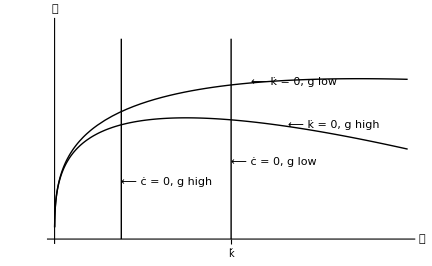

```mathematica
RamseySSPlot=Show[cForKDotEq0Plot,cForKDotEq0HighGrowthPlot
, kbar1Plot,kbar2Plot
,Graphics[Text["⟵ ċ = 0, g low",{kbar1,cbar1/2},{-1,0}]]
,Graphics[Text["⟵ ċ = 0, g high ",{kbar2,cbar2/2},{-1,0}]]
,Graphics[Text["⟵ k̇ = 0, g low",{1.6kbar1, 1.02cbar1},{1,0}]]
,Graphics[Text["⟵ k̇ = 0, g high ",{3.5kbar2, 1.0cbar2},{-1,0}]]
,AxesOrigin->{0.,0.}
,AxesLabel->{"𝓀","𝒸"}
,Ticks->{{{kbar1,"ǩ"}},None}
,PlotRange->{{0.,kMax},{0.,cOfk[kMax]}}
,DisplayFunction->$DisplayFunction
];RamseySSPlot
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["./Figures/RamseySSPlot.eps",RamseySSPlot];
Export["./Figures/RamseySSPlot.pdf",RamseySSPlot];
Export["./Figures/RamseySSPlot.png",RamseySSPlot];
```

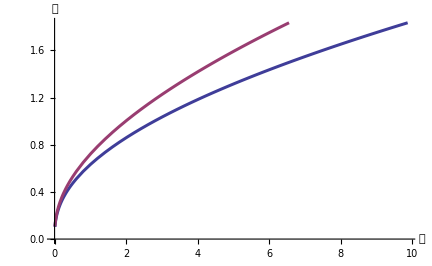

```mathematica
SaddlePathPlot = Plot[{cOfk[kPlot],cOfkHighGrowth[kPlot]},{kPlot,kMin,kMax}
,PlotStyle->Thickness[0.005]
,AxesLabel->{"𝓀","𝒸"}
,PlotRange->{{0.,kMax},{0.,cOfk[kMax]}}
];
SaddlePathPlot
```

```mathematica
TooHi=NDSolve[{c'[t]==CDot[1/3,0.05,0.02,0.02,1.75,.01],k'[t]==KDot[1/3,0.05,0.02,0.01],c[0]==0.65,k[0]==1},{c[t],k[t]}, {t,0,100}];TooLo=NDSolve[{c'[t]==CDot[1/3,0.05,0.02,0.02,1.75,.01],k'[t]==KDot[1/3,0.05,0.02,0.01],c[0]==0.55,k[0]==1},{c[t],k[t]}, {t,0,100}];
```

NDSolve::ndsz: At t == 16.6582, step size is effectively zero; singularity or stiff system suspected.

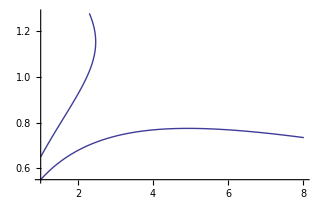

```mathematica
tLoMax = 14;tHiMax=12;TooLoPlotRaw=ParametricPlot[Evaluate[{k[t],c[t]}/.TooLo],{t,0,tLoMax},PlotRange->All,DisplayFunction->Identity];
TooHiPlotRaw = ParametricPlot[Evaluate[{k[t],c[t]}/.TooHi],{t,0,tHiMax},PlotRange->All,DisplayFunction->Identity];
Show[TooLoPlotRaw,TooHiPlotRaw,DisplayFunction->$DisplayFunction]
```

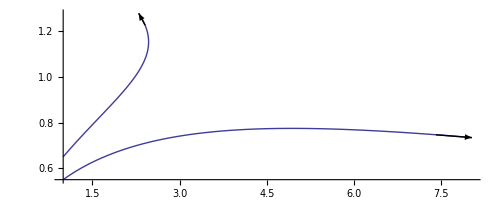

```mathematica
DivergePlot = Show[
TooLoPlotRaw,Graphics[Arrow[{(Evaluate[{k[t],c[t]} /. TooLo] /. t->tLoMax-1)[[1]],(Evaluate[{k[t],c[t]} /. TooLo] /. t->tLoMax)[[1]]}]]
,
TooHiPlotRaw,Graphics[Arrow[{(Evaluate[{k[t],c[t]} /. TooHi] /. t->tHiMax-1)[[1]],(Evaluate[{k[t],c[t]} /. TooHi] /. t->tHiMax)[[1]]}]]
,DisplayFunction->$DisplayFunction
]
```

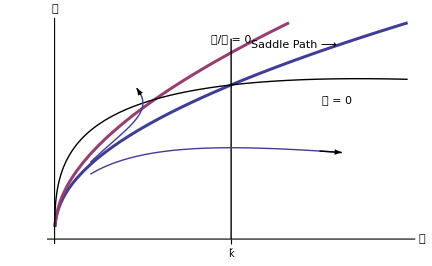

```mathematica
RamseySaddlePlot = Show[
SaddlePathPlot
,kbar1Plot
,cForKDotEq0Plot
,DivergePlot
,Graphics[Text["Saddle Path ⟶   ",{1.6 kbar1,cOfk[1.6 kbar1]},{1,0}]]
,Graphics[Text["𝒸̇/𝒸 = 0",{ kbar1,cOfk[kbar1] 1.3},{0,0}]]
,Graphics[Text["𝓀̇ = 0",{ 0.8kMax,0.9cbar1},{0,0}]]
,AxesLabel->{"𝓀","𝒸"}
,PlotRange->{{0.,kMax},{0.,cOfk[kMax]}}
,Ticks->{{{kbar1,"ǩ"}},None}
,DisplayFunction->$DisplayFunction];RamseySaddlePlot
```

```mathematica
Export["./Figures/RamseySaddlePlot.eps",RamseySaddlePlot];
Export["./Figures/RamseySaddlePlot.pdf",RamseySaddlePlot];
Export["./Figures/RamseySaddlePlot.png",RamseySaddlePlot];
```

```mathematica
cPath = Table[{k,cOfkHighGrowth[k]},{k,kbar2,kbar1,(kbar1-kbar2)/10}];
cPath= AppendTo[cPath,{kbar1,cbar1}];
```

```mathematica
cPathPlot=ListPlot[cPath,PlotStyle->{PointSize[Medium],Red}];
```

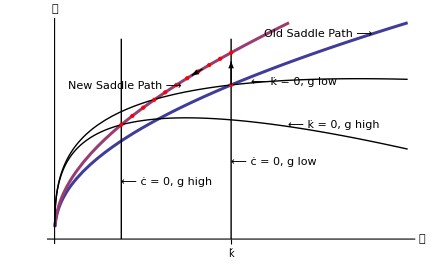

```mathematica
RamseyGrowthRateChange = Show[
SaddlePathPlot
,cForKDotEq0Plot,cForKDotEq0HighGrowthPlot
, kbar1Plot,kbar2Plot
,cPathPlot 
,Graphics[Text["Old Saddle Path ⟶   ",{1.8 kbar1,cOfk[1.8 kbar1]},{1,0}]]
,Graphics[Text["New Saddle Path ⟶   ",{1.9 kbar2,cOfkHighGrowth[1.8 kbar2]},{1,0}]]
,Graphics[Text["⟵ ċ = 0, g low",{kbar1,cbar1/2},{-1,0}]]
,Graphics[Text["⟵ ċ = 0, g high ",{kbar2,cbar2/2},{-1,0}]]
,Graphics[Text["⟵ k̇ = 0, g low",{1.6kbar1, 1.02cbar1},{1,0}]]
,Graphics[Text["⟵ k̇ = 0, g high ",{3.5kbar2,1.0cbar2},{-1,0}]]
,Graphics[Arrow[{{kbar1,cbar1},{kbar1,cbar1+0.2}}]]
,Graphics[Arrow[{{kbar1-0.8,cOfkHighGrowth[kbar1-0.8]},{kbar1-1.1,cOfkHighGrowth[kbar1-1.1]}}]]
,AxesOrigin->{0.,0.}
,AxesLabel->{"𝓀","𝒸"}
,Ticks->{{{kbar1,"ǩ"}},None}
,PlotRange->{{0.,kMax},{0.,cOfk[kMax]}}
,DisplayFunction->$DisplayFunction
];Print[RamseyGrowthRateChange];
```

```mathematica
Export["./Figures/RamseyGrowthRateChange.eps",RamseyGrowthRateChange];
Export["./Figures/RamseyGrowthRateChange.pdf",RamseyGrowthRateChange];
Export["./Figures/RamseyGrowthRateChange.png",RamseyGrowthRateChange];
```

## References

Barro, R. J. and X. Sala-i-Martin (1995). Economic Growth. New York: McGraw-Hill.

Blanchard, O. J., and S. Fischer. 1989. Lectures On Macroeconomics. Cambridge, Mass.: The MIT Press.

Cass, D. 1965. Optimum Growth in an Aggregative Model of Capital Accumulation. Review of Economic Studies 32:233-40.

Kamien, M. I., and N. L. Schwartz. 1991. Dynamic Optimization: The Calculus of Variations and Optimal Control in Economics and Management. 2nd ed. Amsterdam: North-Holland.

King, R. G. and S.T. Rebelo. 1993. Transitional Dynamics and Economic Growth in the Neoclassical model. American Economic Review 4:908-931.

Koopmans, T. C. 1965. On the concept of opitmal economic growth. In: The Econometric Approach to Development Planning. Amsterdam: North Holland.

Mulligan, C.B. and X. Sala-i-Martin. 1991. A note on the time elimination method for solving recursive dynamic economic problems. NBER Working Paper No. 116, Nov.

Ramsey, F. P. 1928. A Mathematical Theory of Saving. The Economic Journal 38 (December):543-59.

Romer, D. 1996. Advanced MacroEconomics. New York: McGraw Hill.

Schwalbe, D. and Wagon, S. 1997. VisualDSolve. Visualizing Differential Equations with Mathematica. New York: TELOS-Springer Verlag.

## ABOUT THE AUTHOR

Alexander Tabarrok is Research Director for the Independent Institute, a non-profit think-tank which conducts research on public policy and is
based in Oakland, CA. He received his Ph.D. in economics from George Mason University, and he has taught at the University of Virginia and Ball State University. Papers by Dr. Tabarrok have appeared in The Journal of Law and Economics, Public Choice, Economic Inquiry, The Journal of Health Economics, The Journal of Theoretical Politics, and many other journals.

Dr. Alexander Tabarrok
Director of Research
The Independent Institute
100 Swan Way
Oakland, CA, 94621-1428
Tel. 510-632-1366
Email: ATabarrok@Independent.org

## ELECTRONIC SUBSCRIPTIONS

Included in the distribution for each electronic subscription is the file Ramsey.nb containing Mathematica code for the material described in this article.